```mathematica
resFun[x0_, x1_, params_]:=Module[{l11,l12,l21,l31},(
l11=params[[1]]*Sin[params[[2]]*x0+params[[3]]]+params[[4]];
l12=params[[5]]*x1^2+params[[6]]*x1+params[[7]];
l21=params[[8]]*Sin[params[[9]]*(l11+l12)+params[[10]]]+params[[11]];
l31=params[[12]]*Exp[params[[13]]*l21]+params[[14]]*l21+params[[15]];
Return[l31])
];
paramsFromGPT={2.24403662*10^-2,3.14159225,3.14159285,-0.127024779,-2.24402905*10^-2,-3.15916354*10^-9,9.87381973*10^-3,0.760834078,2.29485549,3.54827251,-0.119962564,308.83351,25.4620089,-0.119531024,-0.0435317167};
paramsFromRandom={0.43077466,-7.15943922,-7.34528479,-2.07630735,1.91758819,0.01496481,-2.09723196,2.92586628,-0.29131828,-0.23546396,-1.48338538,1.34088731,0.57852638,-2.66637998,1.4920844};
```

```mathematica
arndp=Round[paramsFromGPT,.01]
```

{0.02,3.14,3.14,-0.13,-0.02,0.,0.01,0.76,2.29,3.55,-0.12,308.83,25.46,-0.12,-0.04}

```mathematica
resFun[x0, x1,arndp]//FullSimplify
```

-0.0256+14.55 ⅇ^(19.3496 Sin[3.2752-0.0458 x1^2+0.0458 Sin[3.14+3.14 x0]])-0.0912 Sin[3.2752-0.0458 x1^2+0.0458 Sin[3.14+3.14 x0]]

```mathematica
Plot3D[{Exp[Sin[π x0] + x1^2],resFun[x0, x1,paramsFromGPT],resFun[x0, x1,paramsFromRandom]},{x0,-1,1},{x1,-1,1},PlotStyle->Opacity[.7],PlotLegends->{"Exact","GPT Params","Random Params"}]
```

-Graphics3D-

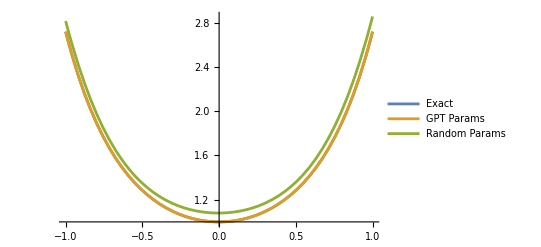

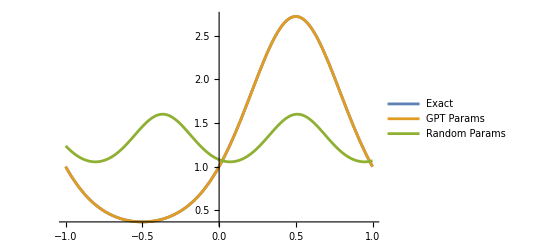

```mathematica
(*Cross-sections along x0=0 and x1=0*)
Plot[{Exp[Sin[π 0] + x1^2],resFun[0, x1,params],resFun[0, x1,params2]},{x1,-1,1},PlotLegends->{"Exact","GPT Params","Random Params"}]
Plot[{Exp[Sin[π x0]],resFun[x0, 0,params],resFun[x0,0,params2]},{x0,-1,1},PlotLegends->{"Exact","GPT Params","Random Params"}]
```